```mathematica
tf[x_]:=Piecewise[{{1, TrueQ[x]}, {0, ¬TrueQ[x]}}]
```

```mathematica
Timing[olist=Monitor[Table[Sum[tf[Mod[x,i]==1],{i,2,x-1}],{x,3,15000}],{x,i}];]
```

{389.42401,Null}

```mathematica
Take[olist,{10,30}]
```

{1,5,1,3,3,4,1,5,1,5,3,3,1,7,2,3,3,5,1,7,1}

```mathematica
DeleteDuplicates[olist]
```

{1,2,3,5,4,7,8,9,11,6,15,14,17,13,19,23,20,29,31,26,27,10,35,24,39,47,41,21,44,12,59,34,53,49,55,63,32,71,25,62}

```mathematica
Table[Min[Flatten[Position[olist,i]]],{i,DeleteDuplicates[olist]}]
```

{1,3,5,11,15,23,35,47,59,63,119,143,179,191,239,359,575,719,839,899,959,1023,1259,1295,1679,2519,2879,3071,3599,4095,5039,5183,6299,6479,6719,7559,9215,10079,12287,14399}

```mathematica
Map[DivisorSigma[0,#]/2&,Delete[Out[50],1]]
```

{1,1,1,2,1,2,1,1,3,2,2,1,1,1,1,3,1,1,2,2,4,1,4,2,2,1,2,2,12,1,2,1,4,1,1,4,1,2,6}

```mathematica
FactorInteger[Out[50]+1]//Column
```

{{2,1}}
{{2,2}}
{{2,1},{3,1}}
{{2,2},{3,1}}
{{2,4}}
{{2,3},{3,1}}
{{2,2},{3,2}}
{{2,4},{3,1}}
{{2,2},{3,1},{5,1}}
{{2,6}}
{{2,3},{3,1},{5,1}}
{{2,4},{3,2}}
{{2,2},{3,2},{5,1}}
{{2,6},{3,1}}
{{2,4},{3,1},{5,1}}
{{2,3},{3,2},{5,1}}
{{2,6},{3,2}}
{{2,4},{3,2},{5,1}}
{{2,3},{3,1},{5,1},{7,1}}
{{2,2},{3,2},{5,2}}
{{2,6},{3,1},{5,1}}
{{2,10}}
{{2,2},{3,2},{5,1},{7,1}}
{{2,4},{3,4}}
{{2,4},{3,1},{5,1},{7,1}}
{{2,3},{3,2},{5,1},{7,1}}
{{2,6},{3,2},{5,1}}
{{2,10},{3,1}}
{{2,4},{3,2},{5,2}}
{{2,12}}
{{2,4},{3,2},{5,1},{7,1}}
{{2,6},{3,4}}
{{2,2},{3,2},{5,2},{7,1}}
{{2,4},{3,4},{5,1}}
{{2,6},{3,1},{5,1},{7,1}}
{{2,3},{3,3},{5,1},{7,1}}
{{2,10},{3,2}}
{{2,5},{3,2},{5,1},{7,1}}
{{2,12},{3,1}}
{{2,6},{3,2},{5,2}}

```mathematica
Select[Out[50],PrimeQ]
```

{3,5,11,23,47,59,179,191,239,359,719,839,1259,2879,5039,6299,6719,7559,10079}

```mathematica
Map[FactorInteger,%+1]//Column
```

{{2,2}}
{{2,1},{3,1}}
{{2,2},{3,1}}
{{2,3},{3,1}}
{{2,4},{3,1}}
{{2,2},{3,1},{5,1}}
{{2,2},{3,2},{5,1}}
{{2,6},{3,1}}
{{2,4},{3,1},{5,1}}
{{2,3},{3,2},{5,1}}
{{2,4},{3,2},{5,1}}
{{2,3},{3,1},{5,1},{7,1}}
{{2,2},{3,2},{5,1},{7,1}}
{{2,6},{3,2},{5,1}}
{{2,4},{3,2},{5,1},{7,1}}
{{2,2},{3,2},{5,2},{7,1}}
{{2,6},{3,1},{5,1},{7,1}}
{{2,3},{3,3},{5,1},{7,1}}
{{2,5},{3,2},{5,1},{7,1}}

```mathematica
ones[x_]:=Sum[tf[Mod[x,i]==1],{i,2,x-1}]
```

```mathematica
ones[5]
```

2

```mathematica
Table[{DivisorSigma[0,n-1]-1,ones[n]},{n,5,20}]
```

{{2,2},{1,1},{3,3},{1,1},{3,3},{2,2},{3,3},{1,1},{5,5},{1,1},{3,3},{3,3},{4,4},{1,1},{5,5},{1,1}}

```mathematica
moreonesthan[n_]=(m0=n;Block[{current=m0,oprev=ones[m0]+1},While[ones[current]<oprev,current++];current])
moreonesthan[5]
```

```mathematica
s[x_]:=x/GCD[x,DivisorSigma[1,x]]
```

```mathematica
ss[y_]:=NestWhile[s,y,s[#]≠#&]
ss[196560]
```

9

```mathematica
Map[ss,Out[50]+1]
```

{2,4,1,3,16,2,36,3,5,64,1,144,5,3,5,4,576,1,7,900,4,1024,5,1296,35,7,5,3,3600,4096,35,5184,225,3,35,21,9216,5,3,14400}

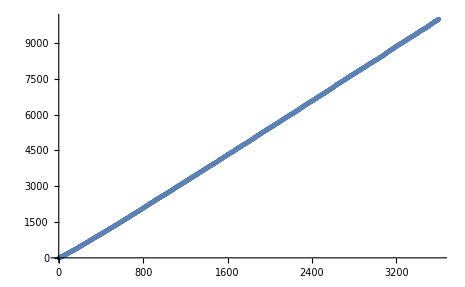

```mathematica
ListPlot[Select[Range[10000],s[#]==#(*∧¬PrimeQ[#]∧¬PrimePowerQ[#]*)&]]
```

```mathematica
sumdigits[n_]:=NestWhile[Total[IntegerDigits[#]]&,n,#≥10&]
sumdigits[196560]
```

9

```mathematica
Clear[k]
```

```mathematica
sssQ[x_]:=If[ss[x]==sumdigits[x],Sow[x]]
Timing[sssqlist=Last[Last[Monitor[Reap[Block[{k=0},For[null=0,k<100000000,k++,sssQ[k]]]],k]]];]
```

{3620.24175,Null}

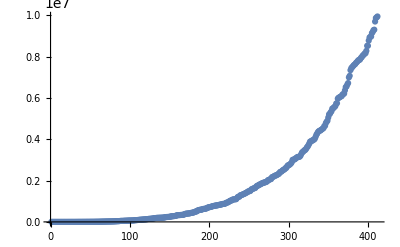

```mathematica
ListPlot[Last[Last[Last[Out[144]]]]]
```

-1.9771×10^7+104724. x

8.08717×10^6-112072. x+281.552 x^2

-1.69061×10^6+39816.2 x-211.27 x^2+0.426685 x^3

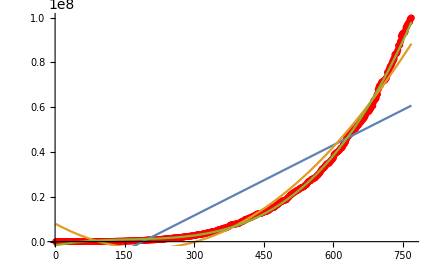

```mathematica
data=sssqlist;
line = Fit[data, {1,x},x]
parabola = Fit[data, {1,x,x^2}, x]
cubic = Fit[data, {1,x,x^2,x^3}, x]
Show[ListPlot[data, PlotStyle->Red,PlotRange->All], Plot[{line, parabola,cubic}, {x, 1, Length[data]},PlotRange->All]]
```

```mathematica
lm=LinearModelFit[data,x^2,x];
lm["BestFit"]
lm[{"RSquared"(*,"FitResiduals"*),"ANOVATable"}]
```

-8.10629×10^6+145.079 x^2

{0.925283, | DF | SS | MS | F-Statistic | P-Value
x^2 | 1 | 5.04368×10^17 | 5.04368×10^17 | 9498.41 | 2.70645158575×10^-434
Error | 767 | 4.07279×10^16 | 5.31003×10^13 |  | 
Total | 768 | 5.45096×10^17 |  |  | }

```mathematica
lm=LinearModelFit[data,x^3,x];
lm["BestFit"]
lm[{"RSquared"(*,"FitResiduals"*),"ANOVATable"}]
```

-2.78819×10^6+0.204727 x^3

{0.986597, | DF | SS | MS | F-Statistic | P-Value
x^3 | 1 | 5.3779×10^17 | 5.3779×10^17 | 56460. | 1.7438316699×10^-720
Error | 767 | 7.3058×10^15 | 9.52516×10^12 |  | 
Total | 768 | 5.45096×10^17 |  |  | }

```mathematica
lm=LinearModelFit[data,x^4,x];
lm["BestFit"]
lm[{"RSquared"(*,"FitResiduals"*),"ANOVATable"}]
```

577485.+0.0002846 x^4

{0.999193, | DF | SS | MS | F-Statistic | P-Value
x^4 | 1 | 5.44656×10^17 | 5.44656×10^17 | 949902. | 1.6007974955×10^-1188
Error | 767 | 4.39784×10^14 | 5.73381×10^11 |  | 
Total | 768 | 5.45096×10^17 |  |  | }

```mathematica
lm=LinearModelFit[data,x^5,x];
lm["BestFit"]
lm[{"RSquared"(*,"FitResiduals"*),"ANOVATable"}]
```

2.98919×10^6+3.90222×10^-7 x^5

{0.987558, | DF | SS | MS | F-Statistic | P-Value
x^5 | 1 | 5.38314×10^17 | 5.38314×10^17 | 60879.4 | 7.10275363207×10^-733
Error | 767 | 6.78204×10^15 | 8.84229×10^12 |  | 
Total | 768 | 5.45096×10^17 |  |  | }

```mathematica
Length[sssqlist]
Length[sssqlist]/100000000//N
```

769

7.69×10^-6

```mathematica
Select[Range[1000000],ss[#]==sumdigits[#]&]
```

{1,2,3,4,5,7,8,9,12,28,40,48,54,84,117,135,140,162,192,216,252,405,432,448,496,540,648,675,702,768,819,1215,1488,1728,1755,1782,1944,2160,2430,2480,2700,2808,3072,3276,3472,3645,3724,3780,4464,4480,4860,4914,5265,5400,5832,7020,7290,7776,8128,8505,8775,11340,12285,12288,13104,14580,14896,15795,17010,17199,18900,19602,19656,20925,21060,22275,23166,24384,25515,28080,28672,31590,34020,35100,36855,40640,47385,49005,49140,49152,52650,54400,56896,57024,58032,61425,63180,64152,65610,66825,66960,68796,70200,73152,78408,83700,84240,89100,92664,94770,102060,103194,105300,109350,110565,116640,117760,120393,125440,125550,136080,140400,147015,147420,148960,155520,158720,162162,167400,181440,185328,189540,194400,196560,196608,198400,200475,200880,202176,205335,206388,210600,221130,228096,235224,238140,238336,243000,245700,252720,267300,272025,275184,279936,283024,289575,294840,314496,326781,328050,328536,331695,334800,336960,340200,343035,356400,368550,392448,396900,400950,406224,408240,412776,421200,435456,441045,442260,459270,467775,491400,502200,504576,544320,561600,567567,585900,588060,589680,602640,623700,628992,631800,637065,648648,663390,690525,705672,707560,722358,725760,741312,758160,765450,773955,786240,786432,798336,801900,808704,821340,825552,839808,842751,852930,868725,870480,872960,882090,915712,933120,943488,950976,982800}

```mathematica
Map[DivisorSigma[0,#]&,Out[112]]
```

{1,2,2,3,2,2,4,3,6,6,8,10,8,12,6,8,12,10,14,16,18,10,20,14,10,24,20,12,16,18,12,12,20,28,16,20,24,40,24,20,36,32,22,36,20,14,18,48,30,32,36,32,20,48,28,48,28,36,14,24,24,60,32,26,60,42,30,24,48,24,72,30,64,24,60,30,40,28,28,80,26,48,72,72,40,28,28,30,96,30,60,48,28,70,60,48,72,56,36,36,80,72,96,42,60,72,100,90,80,56,84,60,90,48,48,84,44,32,60,60,120,120,36,120,72,96,44,80,96,140,100,84,108,160,34,54,42,100,84,36,90,120,96,90,72,108,54,96,144,120,108,48,120,64,45,60,160,128,48,54,72,56,120,140,144,60,150,120,72,135,84,120,140,120,150,108,42,144,72,72,192,120,72,168,168,60,144,108,200,120,180,144,144,60,160,112,60,84,72,80,180,140,140,96,72,224,38,160,126,108,108,150,72,40,72,72,160,80,84,54,126,160,84,240}

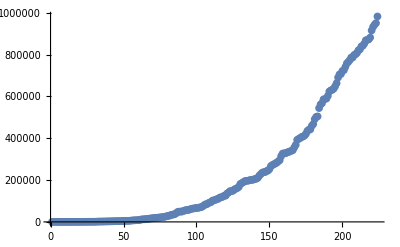

```mathematica
ListPlot[%]
```

```mathematica
Fit[Out[112],{1,x,x^2},x]
```

63108.2-3251.42 x+31.8597 x^2

```mathematica
DivisorSigma[1,196560]
```

```mathematica
GCD[833280,196560]
```

1680

```mathematica
196560/1680
```

```mathematica
DivisorSigma[1,117]
```

```mathematica
DivisorSigma[1,182]
```

```mathematica
GCD[117,336]
```

3

```mathematica
DivisorSigma[1,833280]
```

3139584

```mathematica
FactorInteger[833280]
```

{{2,8},{3,1},{5,1},{7,1},{31,1}}